```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
n=12;L=100;
```

```mathematica
(*Bounds*)
```

```mathematica
(*EdgeCountBound is exact up to Chebyshev*)
```

```mathematica
EdgeCountingBound[nn_,l_,p_,q_]:=Max[1-(8 l^2(1-2q)^-l)/(nn(nn-1)q (1-2p)),0]
```

```mathematica
Table[EdgeCountingBound[1000,l,0.05,0.2],{l,1,10}]
```

{0.999926,0.999506,0.998146,0.994508,0.985697,0.965672,0.922127,0.83048,0.642418,0.264234}

```mathematica
EdgeCountingBound[12,4,0.05,0.25]
```

0

```mathematica
Plot3D[EdgeCountingBound[1000,5,p,q],{p,0,0.5},{q,0,0.5}]
```

-Graphics3D-

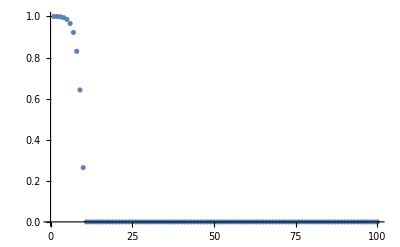

```mathematica
ListPlot[Table[EdgeCountingBound[1000,l,0.05,0.2],{l,1,100}]]
```

```mathematica
Integrate[1/(1/2-2^(k-1)(1/2-q)^k-q),k]
```

-2 (k/(-1+2 q)-Log[1-(1-2 q)^k-2 q]/((-1+2 q) Log[1-2 q]))

```mathematica
((-2 (k/(-1+2 q)-Log[1-(1-2 q)^k-2 q]/((-1+2 q) Log[1-2 q])))/.{k->l-i})-((-2 (k/(-1+2 q)-Log[1-(1-2 q)^k-2 q]/((-1+2 q) Log[1-2 q])))/.{k->2})//FullSimplify
```

(2 ((2+i-l) Log[1-2 q]+Log[1-(1-2 q)^(-i+l)-2 q]-Log[2 (1-2 q) q]))/((-1+2 q) Log[1-2 q])

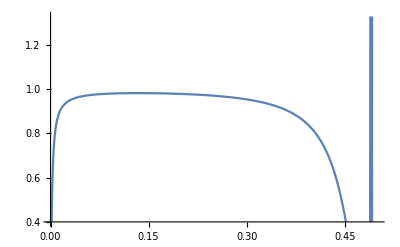

```mathematica
AlignmentsKnownGreedyBoundIntegral[nn_,l_,q_]:=Max[0,Product[1+(2(1-2q)(l-i+1)-2((2 ((2+i-l) Log[1-2 q]+Log[1-(1-2 q)^(-i+l)-2 q]-Log[2 (1-2 q) q]))/((-1+2 q) Log[1-2 q])))/((1-2q)nn(nn-1)),{i,1,l-2}]];
Plot[AlignmentsKnownGreedyBoundIntegral[120,10,q],{q,0,0.5}]
```

```mathematica
qk[q_,k_]=1/2-2^(k-1)(1/2-q)^k;
```

```mathematica
Table[qk[k]-q,{k,1,10}]
```

{-q+qk[1],-q+qk[2],-q+qk[3],-q+qk[4],-q+qk[5],-q+qk[6],-q+qk[7],-q+qk[8],-q+qk[9],-q+qk[10]}

```mathematica
PreBound[nn_,l_,i_,q_]:=(2(1-2q)(l-i+1)-2Sum[1/(qk[q,k]-q),{k,2,l-i}])/((1-2q)nn(nn-1))
```

```mathematica
PreBound[12,5,5,0.3]
```

0.0151515

```mathematica
AlignmentsKnownGreedyBound[nn_,l_,q_]:=Max[Product[1+PreBound[nn,l,i,q],{i,1,l-2}],0]
```

```mathematica
Table[AlignmentsKnownGreedyBound[12,l,0.2],{l,1,100}]
```

{1,1,0.835017,0.60008,0.375908,0.204822,0.096011,0.0379828,0.0123126,0.0031237,0.000574196,0.0000656212,2.94991×10^-6,0,6.68147×10^-9,0,2.51356×10^-10,0,2.79268×10^-11,0,6.2193×10^-12,0,2.3161×10^-12,0,1.29753×10^-12,0,1.02005×10^-12,0,1.07125×10^-12,0,1.44871×10^-12,0,2.45211×10^-12,0,5.07833×10^-12,0,1.26324×10^-11,0,3.71658×10^-11,0,1.27659×10^-10,0,5.06253×10^-10,0,2.29567×10^-9,0,1.18037×10^-8,0,6.83064×10^-8,0,4.41955×10^-7,0,3.17836×10^-6,0,0.0000252715,0,0.000221094,0,0.00211908,0,0.0221621,0,0.251991,0,3.10464,0,41.3185,0,592.3,0,9121.08,0,150516.,0,2.65549×10^6,0,4.99801×10^7,0,1.00152×10^9,0,2.13256×10^10,0,4.81669×10^11,0,1.15204×10^13,0,2.91316×10^14,0,7.77653×10^15,0,2.18832×10^17,0,6.48262×10^18,0,2.01905×10^20,0,6.60339×10^21,0,2.26519×10^23,0}

```mathematica
Plot3D[EdgeCountingBound[1000,5,p,q],{p,0,0.5},{q,0,0.5}]
```

-Graphics3D-

```mathematica
scores=ToAssociations[Import["scores.json"]]
```

<|12→<|0.054→<|0.01→<|correct to i for edgeCountDistance greedy→{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},6,correct at i for edge count order→{0.375,98,0.08}|>,0.02→1|>,6,0.3→<|1|>|>,1,25→1|>
 |  |  |  |

```mathematica
scores[["12"]]
```

<|0.054→<|0.01→<|correct to i for edgeCountDistance greedy→{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},6,correct at i for edge count order→{0.375,0.37,0.26,94,0.045,0.09,0.08}|>,0.02→<|1|>|>,6,0.3→<|1|>|>
 |  |  |  |

```mathematica
listOfScores = Flatten[With[{nlist = PositionIndex[scores]},Table[With[{plist = PositionIndex[scores[[i]]]},Table[With[{qlist = PositionIndex[scores[[i,j]]]},Table[With[{mlist=PositionIndex[scores[[i,j,k]]]},Table[{nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]],scores[[nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]]]]},{l,1,Length[mlist]}]],{k,1,Length[qlist]}]],{j,1,Length[plist]}]],{i,1,Length[nlist]}]],3]
```

{{12,0.054,0.01,correct to i for edgeCountDistance greedy,{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},387,{25,3,{1.,0.99,0.975,0.915,0.87,0.775,0.67,0.61,0.47,82,0.015,0.,0.01,0.015,0.005,0.025,0.02,0.035,0.035}}}
 |  |  |  |

```mathematica
PlotList=ToAssociations[Map[({#[[1]],#[[2]],#[[3]],#[[4]]}->ListPlot[#[[5]]])&,listOfScores]];
```

```mathematica
metricList = {"edgeCountDistance","doublyStochasticMatrixDistance","specDistance","disagreementCount","minDistanceCUDA"};plist = {"0.05","0.1","0.2","0.3","0.4","0.5"};qlist = {"0.01", "0.05","0.1","0.2","0.3"};colors={Blue,Red,Green,Purple,Orange};
```

```mathematica
scores["12","0.05","0.01",StringJoin["correct to i for ",metricList[[i]], " greedy"]]
```

Part::pkspec1: The expression i cannot be used as a part specification.

StringJoin::string: String expected at position 2 in correct to i for <>{edgeCountDistance,doublyStochasticMatrixDistance,specDistance,disagreementCount,minDistanceCUDA}⟦i⟧<> greedy.

Missing[KeyAbsent,correct to i for <>{edgeCountDistance,doublyStochasticMatrixDistance,specDistance,disagreementCount,minDistanceCUDA}⟦i⟧<> greedy]

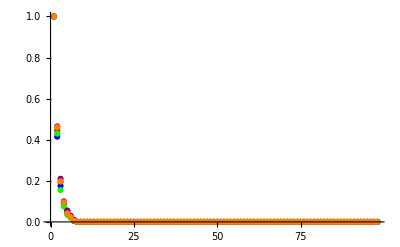

```mathematica
Show[Table[ListPlot[scores["12","0.05","0.01",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

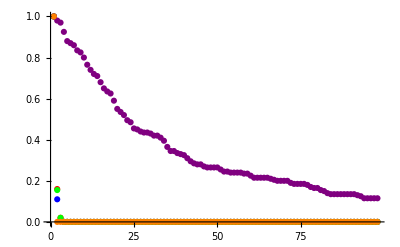

```mathematica
Show[Table[ListPlot[scores["12","0.05","0.2",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

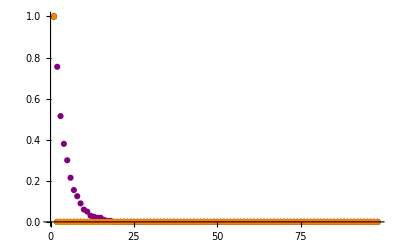

```mathematica
Show[Table[ListPlot[scores["12","0.05","0.3",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

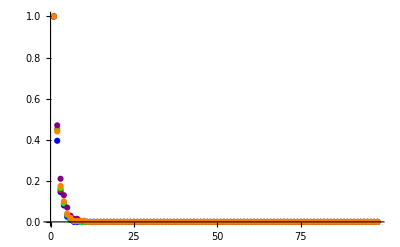

```mathematica
Show[Table[ListPlot[scores["12","0.1","0.01",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

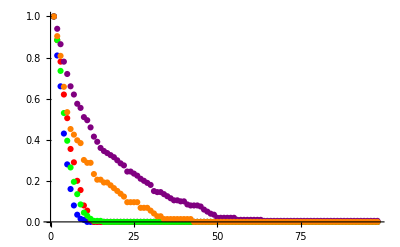

```mathematica
Show[Table[ListPlot[scores["12","0.1","0.05",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

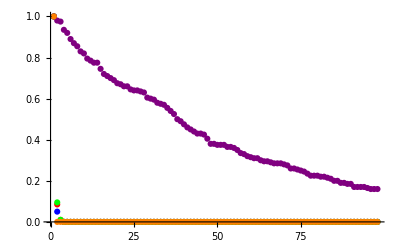

```mathematica
Show[Table[ListPlot[scores["12","0.1","0.2",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

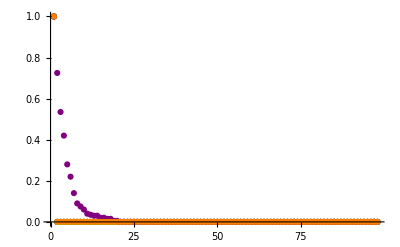

```mathematica
Show[Table[ListPlot[scores["12","0.1","0.3",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

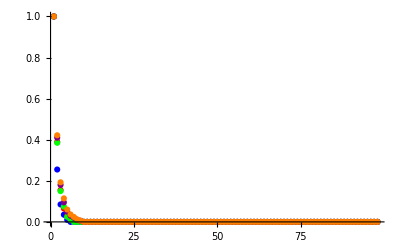

```mathematica
Show[Table[ListPlot[scores["12","0.2","0.01",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

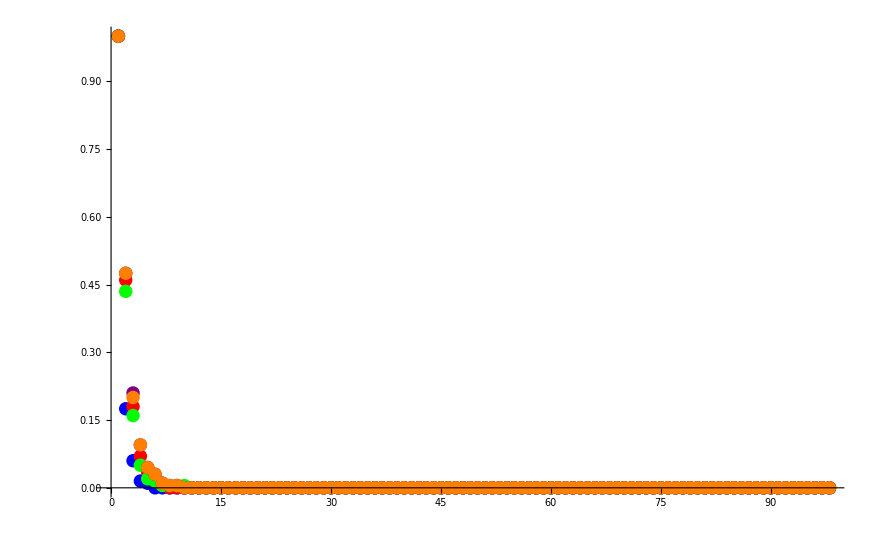

```mathematica
Show[Table[ListPlot[scores["12","0.3","0.01",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

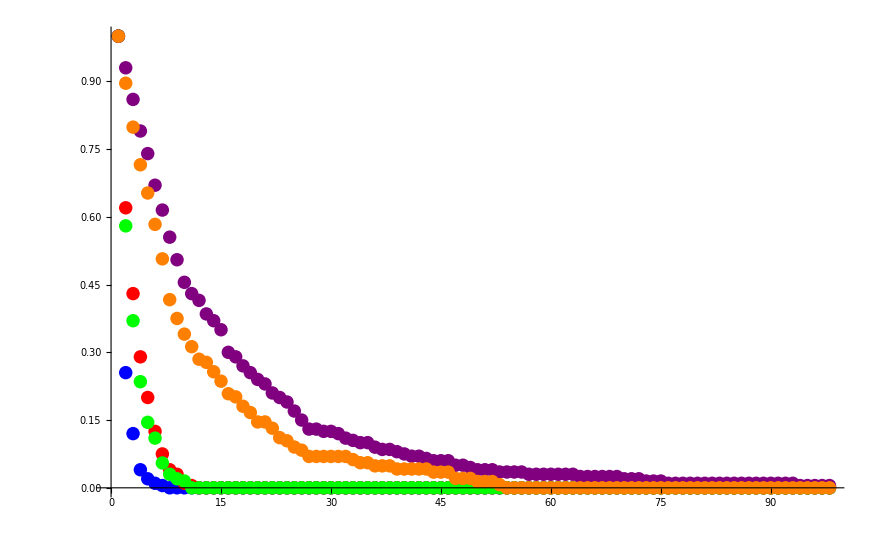

```mathematica
Show[Table[ListPlot[scores["12","0.3","0.05",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

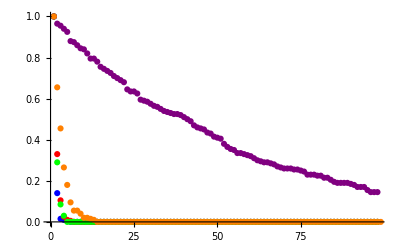

```mathematica
Show[Table[ListPlot[scores["12","0.3","0.1",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

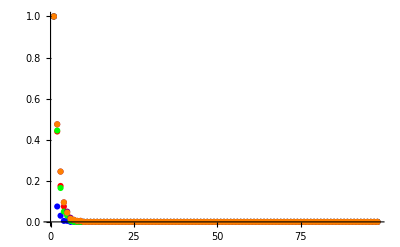

```mathematica
Show[Table[ListPlot[scores["12","0.4","0.01",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

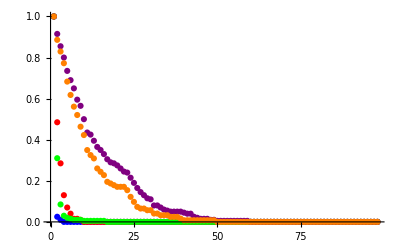

```mathematica
Show[Table[ListPlot[scores["12","0.4","0.05",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

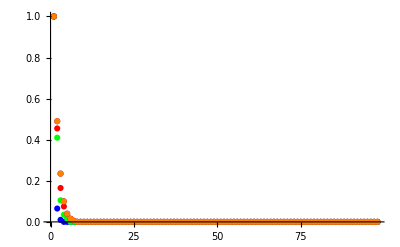

```mathematica
Show[Table[ListPlot[scores["12","0.5","0.01",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

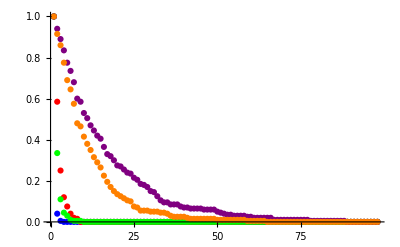

```mathematica
Show[Table[ListPlot[scores["12","0.5","0.05",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

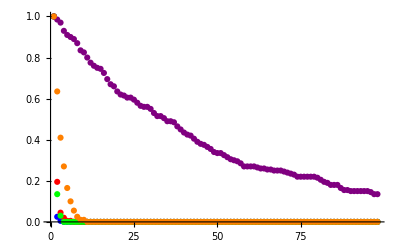

```mathematica
Show[Table[ListPlot[scores["12","0.5","0.1",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

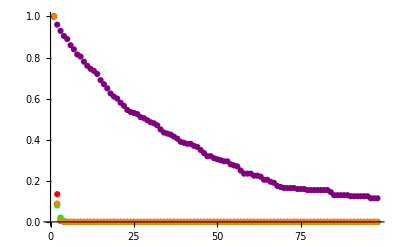

```mathematica
Show[Table[ListPlot[scores["12","0.5","0.2",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

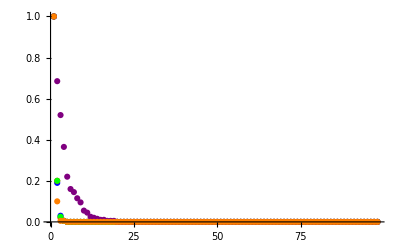

```mathematica
Show[Table[ListPlot[scores["12","0.5","0.3",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

```mathematica
FirstPlots = Table[Show[Check[
Table[ListLogPlot[Map[(10^-5+#)&,scores["12",plist[[a]],qlist[[b]],StringJoin["correct to i for ",metricList[[i]], " greedy"]]],PlotStyle->colors[[i]],PlotRange->Full],{i,1,Length[metricList]}],
Table[ListLogPlot[Map[(10^-5+#)&,scores["12",plist[[a]],qlist[[b]],StringJoin["correct to i for ",metricList[[i]], " greedy"]]],PlotStyle->colors[[i]],PlotRange->Full],{i,1,Length[metricList]-1}]
]],{a,1,Length[plist]},{b,1,Length[qlist]}];
```

ListLogPlot::lpn: Missing[0.00001+KeyAbsent,0.00001+correct to i for minDistanceCUDA greedy] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

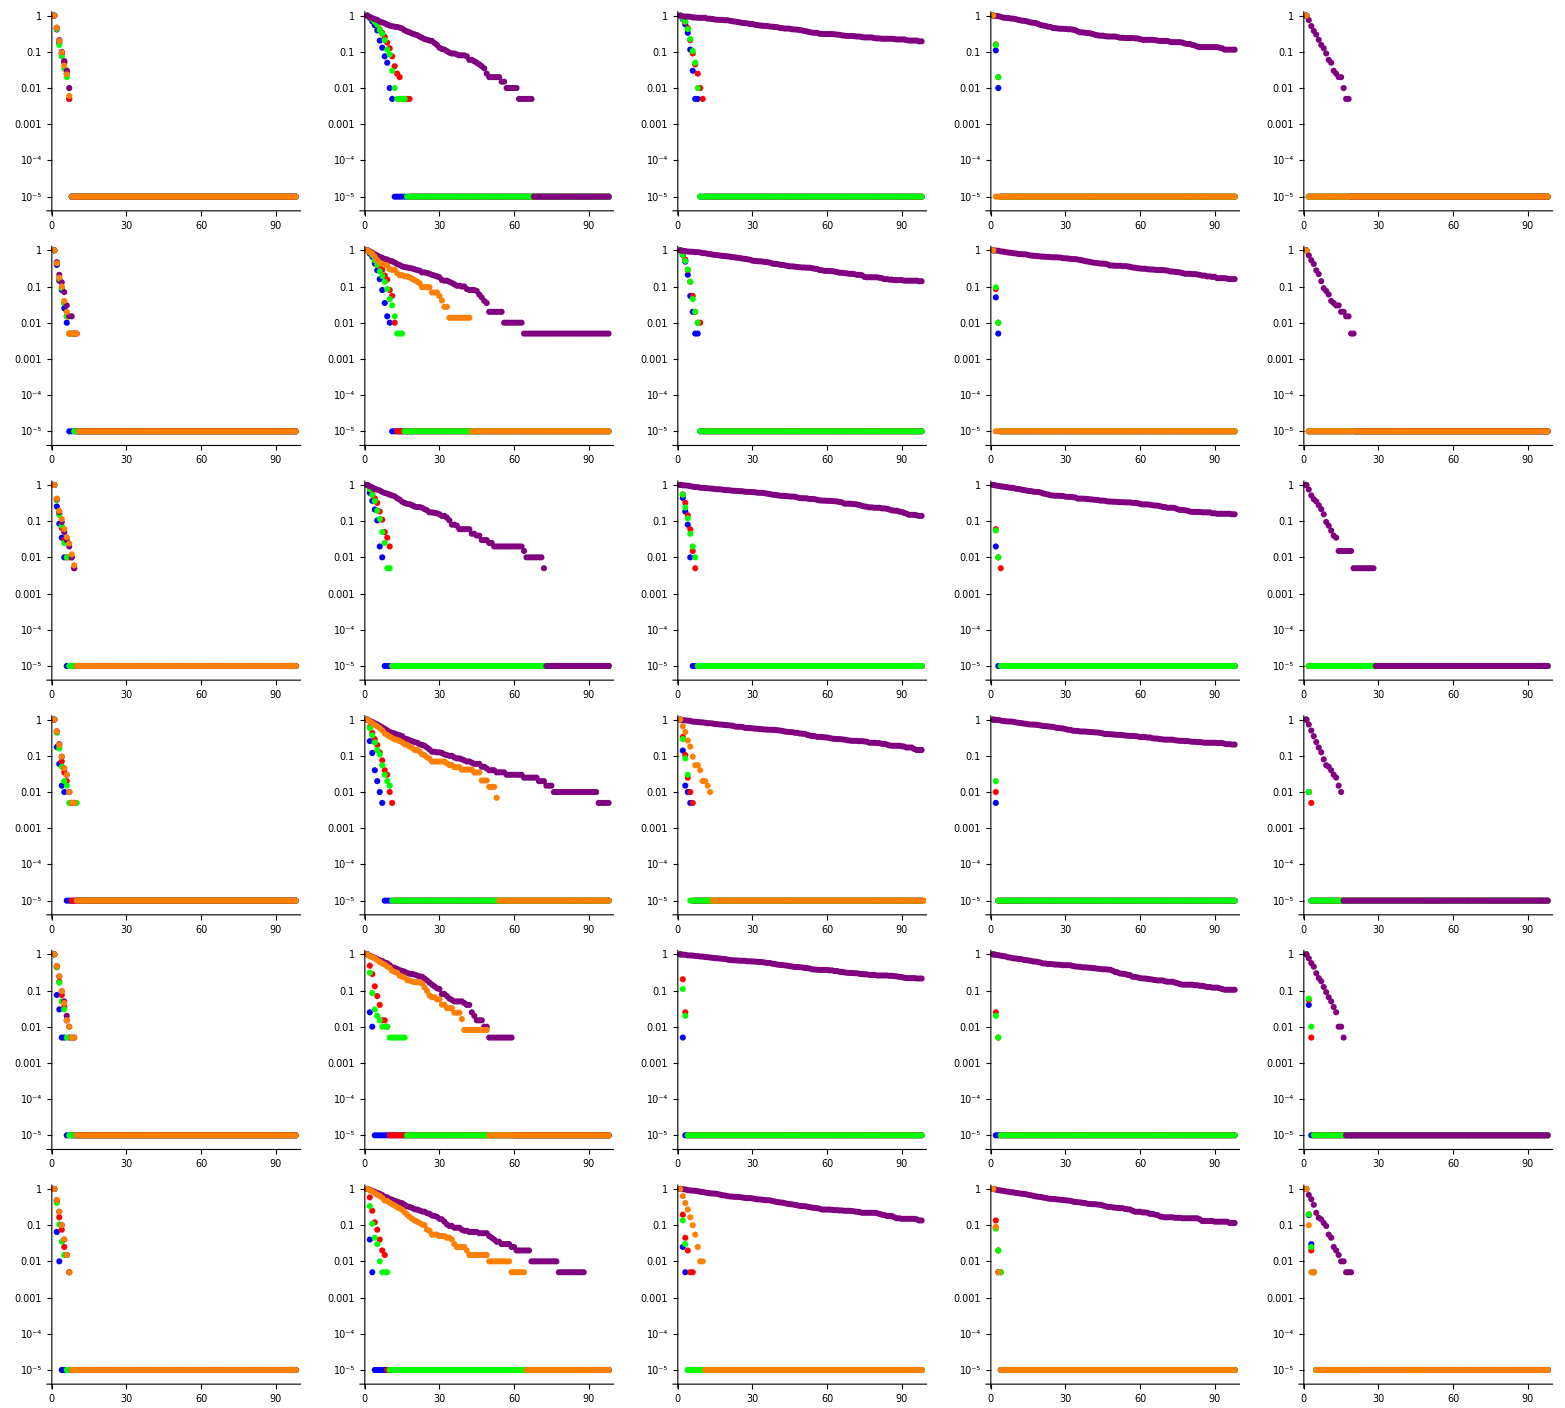
(-Graphics-)

```mathematica
FirstPlots//MatrixForm
```

```mathematica
firstErrorStats=ToAssociations[Import["first_errors.json"]];
```

```mathematica
firstErrorStats[[1]][[1]]
```

<|0.01→<|average first error for disagreementCount greedy→1.925,std of first error for disagreementCount greedy→1.3962,average first error for edgeCountDistance greedy→1.745,std of first error for edgeCountDistance greedy→1.14454,average first error for specDistance greedy→1.795,std of first error for specDistance greedy→1.25418|>,0.02→<|average first error for disagreementCount greedy→3.385,std of first error for disagreementCount greedy→3.03921,average first error for edgeCountDistance greedy→2.265,std of first error for edgeCountDistance greedy→1.57314,average first error for specDistance greedy→2.53,std of first error for specDistance greedy→1.89976|>|>

```mathematica
listOfFES = Flatten[With[{nlist = PositionIndex[firstErrorStats]},Table[With[{plist = PositionIndex[firstErrorStats[[i]]]},Table[With[{qlist = PositionIndex[firstErrorStats[[i,j]]]},Table[With[{mlist=PositionIndex[firstErrorStats[[i,j,k]]]},Table[{nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]],firstErrorStats[[nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]]]]},{l,1,Length[mlist]}]],{k,1,Length[qlist]}]],{j,1,Length[plist]}]],{i,1,Length[nlist]}]],3];
```

```mathematica
ThirdPlots = Show[Table[ListPlot3D[Flatten[Table[{ToExpression[plist[[a]]],ToExpression[qlist[[b]]],firstErrorStats["12",plist[[a]],qlist[[b]],StringJoin["average first error for ",metricList[[i]], " greedy"]]},{a,1,Length[plist]},{b,1,Length[qlist]}],1],PlotStyle->colors[[i]],PlotRange->All],{i,1,Length[metricList]}]]
```

-Graphics3D-

```mathematica
Table[firstErrorStats["12","0.3","0.1",StringJoin["average first error for ",metricList[[i]], " greedy"]],{i,1,5}]
```

{1.17,1.475,1.405,44.84,2.865}

```mathematica
Table[firstErrorStats["12","0.3","0.01",StringJoin["average first error for ",metricList[[i]], " greedy"]],{i,1,5}]
```

{1.26,1.775,1.7,1.875,1.865}

```mathematica
Table[firstErrorStats["12","0.5","0.01",StringJoin["average first error for ",metricList[[i]], " greedy"]],{i,1,5}]
```

{1.075,1.74,1.565,1.885,1.885}

```mathematica
Table[firstErrorStats["12","0.5","0.05",StringJoin["average first error for ",metricList[[i]], " greedy"]],{i,1,5}]
```

{1.045,2.105,1.545,15.705,10.72}

```mathematica
Table[firstErrorStats["12","0.5","0.1",StringJoin["average first error for ",metricList[[i]], " greedy"]],{i,1,5}]
```

{1.03,1.27,1.165,41.545,2.68}

```mathematica
Table[firstErrorStats["12","0.5","0.2",StringJoin["average first error for ",metricList[[i]], " greedy"]],{i,1,5}]
```

{1.09,1.16,1.105,37.18,1.095}

```mathematica
Table[firstErrorStats["12","0.5","0.3",StringJoin["average first error for ",metricList[[i]], " greedy"]],{i,1,5}]
```

{1.225,1.225,1.23,3.5,1.11}

```mathematica
HamRes=Import["HamiltonianResults.mx"]
```

```mathematica
HamRes
```

```mathematica
scoreListHam=ToAssociations[HamRes[[1]]]
```

Part::partd: Part specification ⟦1⟧ is longer than depth of object.

⟦1⟧

```mathematica
scoreListHam[{"12","0.3","0.01","specDistance"}][[1]]
```

{12,0.3,0.01,specDistance}

```mathematica
Table[Show[Table[ListPlot[scoreListHam[{"12",plist[[a]],qlist[[b]],metricList[[i]]}][[2]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}],PlotRange->{{0,100},{0,1}}],{a,1,6},{b,1,5}]
```

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.01,edgeCountDistance}] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: ⟦1⟧[{12,0.05,0.01,edgeCountDistance}]⟦2⟧ is not a list of numbers or pairs of numbers.

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.01,doublyStochasticMatrixDistance}] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: ⟦1⟧[{12,0.05,0.01,doublyStochasticMatrixDistance}]⟦2⟧ is not a list of numbers or pairs of numbers.

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.01,specDistance}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: ⟦1⟧[{12,0.05,0.01,specDistance}]⟦2⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.01,edgeCountDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.01,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.01,specDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.01,disagreementCount}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.01,minDistanceCUDA}]⟦2⟧,PlotStyle→color]},PlotRange→{{0,100},{0,1}}].

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.05,edgeCountDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.05,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.05,specDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.05,disagreementCount}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.05,minDistanceCUDA}]⟦2⟧,PlotStyle→color]},PlotRange→{{0,100},{0,1}}].

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.1,edgeCountDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.1,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.1,specDistance}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.1,disagreementCount}]⟦2⟧,PlotStyle→color],ListPlot[⟦1⟧[{12,0.05,0.1,minDistanceCUDA}]⟦2⟧,PlotStyle→color]},PlotRange→{{0,100},{0,1}}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

{{Show[{ListPlot[⟦1⟧[{12,0.05,0.01,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.05,0.01,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.05,0.01,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.05,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.05,0.01,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.05,0.05,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.05,0.05,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.05,0.05,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.05,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.05,0.05,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.05,0.1,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.05,0.1,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.05,0.1,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.05,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.05,0.1,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.05,0.2,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.05,0.2,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.05,0.2,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.05,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.05,0.2,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.05,0.3,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.05,0.3,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.05,0.3,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.05,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.05,0.3,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.1,0.01,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.1,0.01,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.1,0.01,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.1,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.1,0.01,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.1,0.05,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.1,0.05,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.1,0.05,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.1,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.1,0.05,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.1,0.1,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.1,0.1,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.1,0.1,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.1,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.1,0.1,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.1,0.2,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.1,0.2,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.1,0.2,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.1,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.1,0.2,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.1,0.3,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.1,0.3,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.1,0.3,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.1,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.1,0.3,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.2,0.01,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.2,0.01,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.2,0.01,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.2,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.2,0.01,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.2,0.05,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.2,0.05,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.2,0.05,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.2,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.2,0.05,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.2,0.1,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.2,0.1,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.2,0.1,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.2,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.2,0.1,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.2,0.2,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.2,0.2,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.2,0.2,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.2,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.2,0.2,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.2,0.3,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.2,0.3,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.2,0.3,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.2,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.2,0.3,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.3,0.01,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.3,0.01,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.3,0.01,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.3,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.3,0.01,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.3,0.05,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.3,0.05,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.3,0.05,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.3,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.3,0.05,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.3,0.1,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.3,0.1,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.3,0.1,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.3,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.3,0.1,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.3,0.2,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.3,0.2,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.3,0.2,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.3,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.3,0.2,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.3,0.3,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.3,0.3,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.3,0.3,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.3,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.3,0.3,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.4,0.01,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.4,0.01,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.4,0.01,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.4,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.4,0.01,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.4,0.05,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.4,0.05,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.4,0.05,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.4,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.4,0.05,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.4,0.1,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.4,0.1,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.4,0.1,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.4,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.4,0.1,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.4,0.2,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.4,0.2,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.4,0.2,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.4,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.4,0.2,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.4,0.3,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.4,0.3,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.4,0.3,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.4,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.4,0.3,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.5,0.01,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.5,0.01,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.5,0.01,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.5,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.5,0.01,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.5,0.05,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.5,0.05,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.5,0.05,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.5,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.5,0.05,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.5,0.1,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.5,0.1,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.5,0.1,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.5,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.5,0.1,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.5,0.2,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.5,0.2,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.5,0.2,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.5,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.5,0.2,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.5,0.3,edgeCountDistance}]⟦2⟧,PlotStyle→RGBColor[0, 0, 1]],ListPlot[⟦1⟧[{12,0.5,0.3,doublyStochasticMatrixDistance}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],ListPlot[⟦1⟧[{12,0.5,0.3,specDistance}]⟦2⟧,PlotStyle→RGBColor[0, 1, 0]],ListPlot[⟦1⟧[{12,0.5,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListPlot[⟦1⟧[{12,0.5,0.3,minDistanceCUDA}]⟦2⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→{{0,100},{0,1}}]}}

```mathematica
Table[Show[Table[ListLogPlot[Map[10^-5+#&,scoreListHam[{"12",plist[[a]],qlist[[b]],metricList[[i]]}][[2]]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}],PlotRange->Full],{a,1,6},{b,1,5}]
```

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.01,edgeCountDistance}] does not exist.

Part::pkspec1: The expression 200001/100000 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLogPlot::lpn: (0.00001+⟦1⟧[{12,0.05,0.01,edgeCountDistance}])⟦200001/100000⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.01,doublyStochasticMatrixDistance}] does not exist.

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.01,specDistance}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,specDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,disagreementCount}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→color]},PlotRange→Full].

Show::gcomb: Could not combine the graphics objects in Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,specDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,disagreementCount}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→color]},PlotRange→Full].

Show::gcomb: Could not combine the graphics objects in Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,specDistance}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,disagreementCount}])⟦200001/100000⟧,PlotStyle→color],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→color]},PlotRange→Full].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

{{Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.01,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.05,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.1,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.2,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.2,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.2,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.2,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.2,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.3,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.3,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.3,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.3,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.05,0.3,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full]},{Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.01,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.01,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.01,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.01,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.01,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.05,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.05,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.05,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.05,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.05,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.1,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.1,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.1,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.1,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.1,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.2,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.2,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.2,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.2,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.2,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.3,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.3,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.3,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.3,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.1,0.3,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full]},{Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.01,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.01,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.01,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.01,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.01,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.05,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.05,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.05,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.05,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.05,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.1,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.1,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.1,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.1,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.1,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.2,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.2,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.2,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.2,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.2,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.3,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.3,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.3,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.3,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.2,0.3,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full]},{Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.01,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.01,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.01,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.01,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.01,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.05,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.05,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.05,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.05,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.05,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.1,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.1,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.1,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.1,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.1,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.2,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.2,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.2,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.2,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.2,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.3,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.3,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.3,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.3,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.3,0.3,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full]},{Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.01,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.01,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.01,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.01,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.01,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.05,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.05,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.05,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.05,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.05,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.1,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.1,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.1,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.1,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.1,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.2,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.2,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.2,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.2,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.2,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.3,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.3,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.3,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.3,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.4,0.3,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full]},{Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.01,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.01,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.01,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.01,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.01,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.05,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.05,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.05,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.05,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.05,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.1,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.1,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.1,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.1,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.1,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.2,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.2,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.2,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.2,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.2,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full],Show[{ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.3,edgeCountDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 0, 1]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.3,doublyStochasticMatrixDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.3,specDistance}])⟦200001/100000⟧,PlotStyle→RGBColor[0, 1, 0]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.3,disagreementCount}])⟦200001/100000⟧,PlotStyle→RGBColor[0.5, 0, 0.5]],ListLogPlot[(1/100000+⟦1⟧[{12,0.5,0.3,minDistanceCUDA}])⟦200001/100000⟧,PlotStyle→RGBColor[1, 0.5, 0]]},PlotRange→Full]}}

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.01,disagreementCount}] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: ⟦1⟧[{12,0.05,0.01,disagreementCount}]⟦2⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.01,disagreementCount}]⟦2⟧,PlotStyle→color],},PlotRange→{{0,100},{0,1}}].

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.05,disagreementCount}] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: ⟦1⟧[{12,0.05,0.05,disagreementCount}]⟦2⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.05,disagreementCount}]⟦2⟧,PlotStyle→color],},PlotRange→{{0,100},{0,1}}].

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.1,disagreementCount}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: ⟦1⟧[{12,0.05,0.1,disagreementCount}]⟦2⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.1,disagreementCount}]⟦2⟧,PlotStyle→color],},PlotRange→{{0,100},{0,1}}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

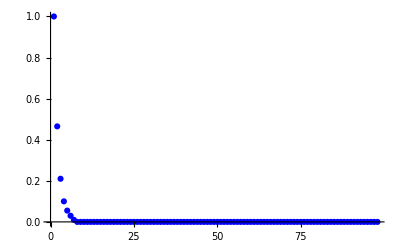
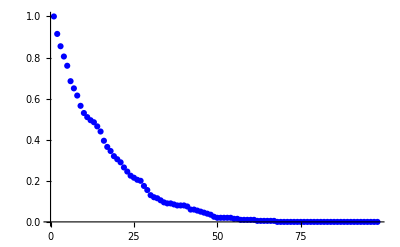
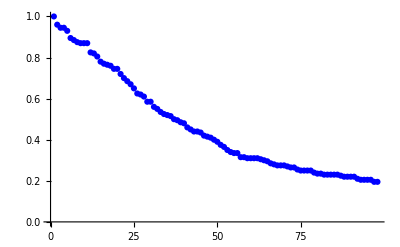
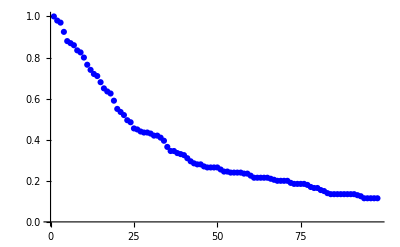
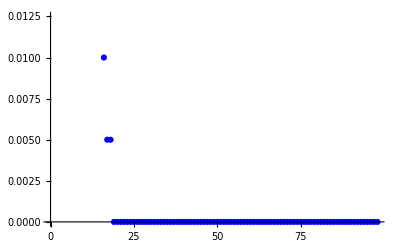
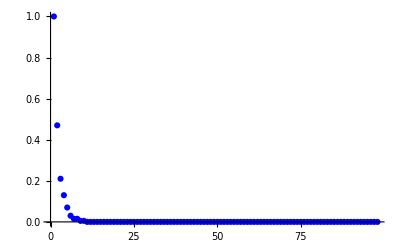
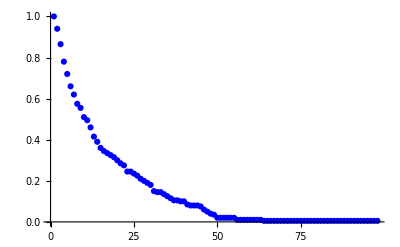
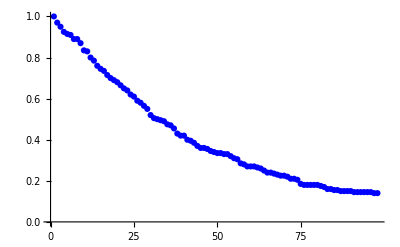
{{Show[{ListPlot[⟦1⟧[{12,0.05,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.05,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.05,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.05,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.05,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.1,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.1,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.1,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.1,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.1,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.2,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.2,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.2,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.2,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.2,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.3,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.3,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.3,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.3,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.3,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.4,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.4,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.4,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.4,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.4,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}]},{Show[{ListPlot[⟦1⟧[{12,0.5,0.01,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.5,0.05,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.5,0.1,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.5,0.2,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}],Show[{ListPlot[⟦1⟧[{12,0.5,0.3,disagreementCount}]⟦2⟧,PlotStyle→RGBColor[1, 0, 0]],-Graphics-},PlotRange→{{0,100},{0,1}}]}}

```mathematica
Table[Show[{ListPlot[scoreListHam[{"12",plist[[a]],qlist[[b]],metricList[[4]]}][[2]],PlotStyle->Red],ListPlot[scores["12",plist[[a]],qlist[[b]],StringJoin["correct to i for ",metricList[[4]], " greedy"]],PlotStyle->Blue]},PlotRange->{{0,100},{0,1}}],{a,1,6},{b,1,5}]
```

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.01,minDistanceCUDA}] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: ⟦1⟧[{12,0.05,0.01,minDistanceCUDA}]⟦2⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.01,minDistanceCUDA}]⟦2⟧,PlotStyle→color],},PlotRange→{{0,100},{0,1}}].

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.05,minDistanceCUDA}] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: ⟦1⟧[{12,0.05,0.05,minDistanceCUDA}]⟦2⟧ is not a list of numbers or pairs of numbers.

ListPlot::lpn: Missing[KeyAbsent,correct to i for minDistanceCUDA greedy] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.05,minDistanceCUDA}]⟦2⟧,PlotStyle→color],ListPlot[Missing[KeyAbsent,correct to i for minDistanceCUDA greedy],PlotStyle→color]},PlotRange→{{0,100},{0,1}}].

Part::partw: Part 2 of ⟦1⟧[{12,0.05,0.1,minDistanceCUDA}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[⟦1⟧[{12,0.05,0.1,minDistanceCUDA}]⟦2⟧,PlotStyle→color],ListPlot[Missing[KeyAbsent,correct to i for minDistanceCUDA greedy],PlotStyle→color]},PlotRange→{{0,100},{0,1}}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

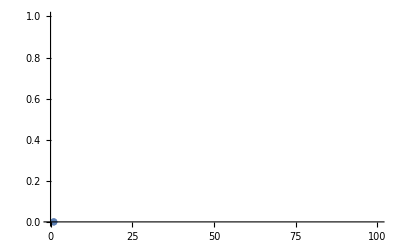
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Check[Show[{ListPlot[scoreListHam[{"12",plist[[a]],qlist[[b]],metricList[[5]]}][[2]],PlotStyle->Red],ListPlot[scores["12",plist[[a]],qlist[[b]],StringJoin["correct to i for ",metricList[[5]], " greedy"]],PlotStyle->Blue]},PlotRange->{{0,100},{0,1}}],ListPlot[{0},PlotRange->{{0,100},{0,1}}]],{a,1,6},{b,1,5}]
```

```mathematica
firstFailureListHam =ToAssociations[HamRes[[2]]]
```

Part::partd: Part specification ⟦2⟧ is longer than depth of object.

⟦2⟧

```mathematica
listOfFESHam=With[{keyList = PositionIndex[firstFailureListHam]},Table[Join[keyList[[i,1]],firstFailureListHam[keyList[[i,1]]]],{i,1,Length[keyList]}]];
```

PositionIndex::invrp: The argument ⟦2⟧ is not a valid Association or a list.

```mathematica
listOfFESHam[[1]]
```

Join[,⟦2⟧[]]

```mathematica
ThirdPlotsHam =Show[ Table[ListPlot3D[Flatten[Table[{ToExpression[plist[[a]]],ToExpression[qlist[[b]]],firstFailureListHam[{"12",plist[[a]],qlist[[b]],metricList[[i]]}][[1]]},{a,1,Length[plist]},{b,1,Length[qlist]}],1],PlotStyle->colors[[i]],PlotRange->All],{i,1,Length[metricList]}]]
```

ListPlot3D::arrayerr: {{0.05,0.01,{12,0.05,0.01,edgeCountDistance}},{0.05,0.05,{12,0.05,0.05,edgeCountDistance}},{0.05,0.1,{12,0.05,0.1,edgeCountDistance}},{0.05,0.2,{12,0.05,0.2,edgeCountDistance}},{0.05,0.3,{12,0.05,0.3,edgeCountDistance}},{0.1,0.01,{12,0.1,0.01,edgeCountDistance}},{0.1,0.05,{12,0.1,0.05,edgeCountDistance}},{0.1,0.1,{12,0.1,0.1,edgeCountDistance}},{0.1,0.2,{12,0.1,0.2,edgeCountDistance}},{0.1,0.3,{12,0.1,0.3,edgeCountDistance}},«20»} must be a valid array or a list of valid arrays.

ListPlot3D::arrayerr: {{0.05,0.01,{12,0.05,0.01,doublyStochasticMatrixDistance}},{0.05,0.05,{12,0.05,0.05,doublyStochasticMatrixDistance}},{0.05,0.1,{12,0.05,0.1,doublyStochasticMatrixDistance}},{0.05,0.2,{12,0.05,0.2,doublyStochasticMatrixDistance}},{0.05,0.3,{12,0.05,0.3,doublyStochasticMatrixDistance}},«1»,{0.1,0.05,{12,0.1,0.05,doublyStochasticMatrixDistance}},{0.1,0.1,{12,0.1,0.1,doublyStochasticMatrixDistance}},{0.1,0.2,{12,0.1,0.2,doublyStochasticMatrixDistance}},{0.1,0.3,{12,0.1,0.3,doublyStochasticMatrixDistance}},«20»} must be a valid array or a list of valid arrays.

ListPlot3D::arrayerr: {{0.05,0.01,{12,0.05,0.01,specDistance}},{0.05,0.05,{12,0.05,0.05,specDistance}},{0.05,0.1,{12,0.05,0.1,specDistance}},{0.05,0.2,{12,0.05,0.2,specDistance}},{0.05,0.3,{12,0.05,0.3,specDistance}},{0.1,0.01,{12,0.1,0.01,specDistance}},{0.1,0.05,{12,0.1,0.05,specDistance}},{0.1,0.1,{12,0.1,0.1,specDistance}},{0.1,0.2,{12,0.1,0.2,specDistance}},{0.1,0.3,{12,0.1,0.3,specDistance}},«20»} must be a valid array or a list of valid arrays.

General::stop: Further output of ListPlot3D::arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot3D[{{0.05,0.01,{12,0.05,0.01,edgeCountDistance}},{0.05,0.05,{12,0.05,0.05,edgeCountDistance}},{0.05,0.1,{12,0.05,0.1,edgeCountDistance}},{0.05,0.2,{12,0.05,0.2,edgeCountDistance}},{0.05,0.3,{12,0.05,0.3,edgeCountDistance}},{0.1,0.01,{12,0.1,0.01,edgeCountDistance}},{0.1,0.05,{12,0.1,0.05,edgeCountDistance}},{0.1,0.1,{12,0.1,0.1,edgeCountDistance}},{0.1,0.2,{12,0.1,0.2,edgeCountDistance}},{0.1,0.3,{12,0.1,0.3,edgeCountDistance}},«20»},PlotStyle→color,PlotRange→All],«3»,ListPlot3D[{«1»},PlotStyle→color,PlotRange→All]}].

Show[{ListPlot3D[{{0.05,0.01,{12,0.05,0.01,edgeCountDistance}},{0.05,0.05,{12,0.05,0.05,edgeCountDistance}},{0.05,0.1,{12,0.05,0.1,edgeCountDistance}},{0.05,0.2,{12,0.05,0.2,edgeCountDistance}},{0.05,0.3,{12,0.05,0.3,edgeCountDistance}},{0.1,0.01,{12,0.1,0.01,edgeCountDistance}},{0.1,0.05,{12,0.1,0.05,edgeCountDistance}},{0.1,0.1,{12,0.1,0.1,edgeCountDistance}},{0.1,0.2,{12,0.1,0.2,edgeCountDistance}},{0.1,0.3,{12,0.1,0.3,edgeCountDistance}},{0.2,0.01,{12,0.2,0.01,edgeCountDistance}},{0.2,0.05,{12,0.2,0.05,edgeCountDistance}},{0.2,0.1,{12,0.2,0.1,edgeCountDistance}},{0.2,0.2,{12,0.2,0.2,edgeCountDistance}},{0.2,0.3,{12,0.2,0.3,edgeCountDistance}},{0.3,0.01,{12,0.3,0.01,edgeCountDistance}},{0.3,0.05,{12,0.3,0.05,edgeCountDistance}},{0.3,0.1,{12,0.3,0.1,edgeCountDistance}},{0.3,0.2,{12,0.3,0.2,edgeCountDistance}},{0.3,0.3,{12,0.3,0.3,edgeCountDistance}},{0.4,0.01,{12,0.4,0.01,edgeCountDistance}},{0.4,0.05,{12,0.4,0.05,edgeCountDistance}},{0.4,0.1,{12,0.4,0.1,edgeCountDistance}},{0.4,0.2,{12,0.4,0.2,edgeCountDistance}},{0.4,0.3,{12,0.4,0.3,edgeCountDistance}},{0.5,0.01,{12,0.5,0.01,edgeCountDistance}},{0.5,0.05,{12,0.5,0.05,edgeCountDistance}},{0.5,0.1,{12,0.5,0.1,edgeCountDistance}},{0.5,0.2,{12,0.5,0.2,edgeCountDistance}},{0.5,0.3,{12,0.5,0.3,edgeCountDistance}}},PlotStyle→RGBColor[0, 0, 1],PlotRange→All],ListPlot3D[{{0.05,0.01,{12,0.05,0.01,doublyStochasticMatrixDistance}},{0.05,0.05,{12,0.05,0.05,doublyStochasticMatrixDistance}},{0.05,0.1,{12,0.05,0.1,doublyStochasticMatrixDistance}},{0.05,0.2,{12,0.05,0.2,doublyStochasticMatrixDistance}},{0.05,0.3,{12,0.05,0.3,doublyStochasticMatrixDistance}},{0.1,0.01,{12,0.1,0.01,doublyStochasticMatrixDistance}},{0.1,0.05,{12,0.1,0.05,doublyStochasticMatrixDistance}},{0.1,0.1,{12,0.1,0.1,doublyStochasticMatrixDistance}},{0.1,0.2,{12,0.1,0.2,doublyStochasticMatrixDistance}},{0.1,0.3,{12,0.1,0.3,doublyStochasticMatrixDistance}},{0.2,0.01,{12,0.2,0.01,doublyStochasticMatrixDistance}},{0.2,0.05,{12,0.2,0.05,doublyStochasticMatrixDistance}},{0.2,0.1,{12,0.2,0.1,doublyStochasticMatrixDistance}},{0.2,0.2,{12,0.2,0.2,doublyStochasticMatrixDistance}},{0.2,0.3,{12,0.2,0.3,doublyStochasticMatrixDistance}},{0.3,0.01,{12,0.3,0.01,doublyStochasticMatrixDistance}},{0.3,0.05,{12,0.3,0.05,doublyStochasticMatrixDistance}},{0.3,0.1,{12,0.3,0.1,doublyStochasticMatrixDistance}},{0.3,0.2,{12,0.3,0.2,doublyStochasticMatrixDistance}},{0.3,0.3,{12,0.3,0.3,doublyStochasticMatrixDistance}},{0.4,0.01,{12,0.4,0.01,doublyStochasticMatrixDistance}},{0.4,0.05,{12,0.4,0.05,doublyStochasticMatrixDistance}},{0.4,0.1,{12,0.4,0.1,doublyStochasticMatrixDistance}},{0.4,0.2,{12,0.4,0.2,doublyStochasticMatrixDistance}},{0.4,0.3,{12,0.4,0.3,doublyStochasticMatrixDistance}},{0.5,0.01,{12,0.5,0.01,doublyStochasticMatrixDistance}},{0.5,0.05,{12,0.5,0.05,doublyStochasticMatrixDistance}},{0.5,0.1,{12,0.5,0.1,doublyStochasticMatrixDistance}},{0.5,0.2,{12,0.5,0.2,doublyStochasticMatrixDistance}},{0.5,0.3,{12,0.5,0.3,doublyStochasticMatrixDistance}}},PlotStyle→RGBColor[1, 0, 0],PlotRange→All],ListPlot3D[{{0.05,0.01,{12,0.05,0.01,specDistance}},{0.05,0.05,{12,0.05,0.05,specDistance}},{0.05,0.1,{12,0.05,0.1,specDistance}},{0.05,0.2,{12,0.05,0.2,specDistance}},{0.05,0.3,{12,0.05,0.3,specDistance}},{0.1,0.01,{12,0.1,0.01,specDistance}},{0.1,0.05,{12,0.1,0.05,specDistance}},{0.1,0.1,{12,0.1,0.1,specDistance}},{0.1,0.2,{12,0.1,0.2,specDistance}},{0.1,0.3,{12,0.1,0.3,specDistance}},{0.2,0.01,{12,0.2,0.01,specDistance}},{0.2,0.05,{12,0.2,0.05,specDistance}},{0.2,0.1,{12,0.2,0.1,specDistance}},{0.2,0.2,{12,0.2,0.2,specDistance}},{0.2,0.3,{12,0.2,0.3,specDistance}},{0.3,0.01,{12,0.3,0.01,specDistance}},{0.3,0.05,{12,0.3,0.05,specDistance}},{0.3,0.1,{12,0.3,0.1,specDistance}},{0.3,0.2,{12,0.3,0.2,specDistance}},{0.3,0.3,{12,0.3,0.3,specDistance}},{0.4,0.01,{12,0.4,0.01,specDistance}},{0.4,0.05,{12,0.4,0.05,specDistance}},{0.4,0.1,{12,0.4,0.1,specDistance}},{0.4,0.2,{12,0.4,0.2,specDistance}},{0.4,0.3,{12,0.4,0.3,specDistance}},{0.5,0.01,{12,0.5,0.01,specDistance}},{0.5,0.05,{12,0.5,0.05,specDistance}},{0.5,0.1,{12,0.5,0.1,specDistance}},{0.5,0.2,{12,0.5,0.2,specDistance}},{0.5,0.3,{12,0.5,0.3,specDistance}}},PlotStyle→RGBColor[0, 1, 0],PlotRange→All],ListPlot3D[{{0.05,0.01,{12,0.05,0.01,disagreementCount}},{0.05,0.05,{12,0.05,0.05,disagreementCount}},{0.05,0.1,{12,0.05,0.1,disagreementCount}},{0.05,0.2,{12,0.05,0.2,disagreementCount}},{0.05,0.3,{12,0.05,0.3,disagreementCount}},{0.1,0.01,{12,0.1,0.01,disagreementCount}},{0.1,0.05,{12,0.1,0.05,disagreementCount}},{0.1,0.1,{12,0.1,0.1,disagreementCount}},{0.1,0.2,{12,0.1,0.2,disagreementCount}},{0.1,0.3,{12,0.1,0.3,disagreementCount}},{0.2,0.01,{12,0.2,0.01,disagreementCount}},{0.2,0.05,{12,0.2,0.05,disagreementCount}},{0.2,0.1,{12,0.2,0.1,disagreementCount}},{0.2,0.2,{12,0.2,0.2,disagreementCount}},{0.2,0.3,{12,0.2,0.3,disagreementCount}},{0.3,0.01,{12,0.3,0.01,disagreementCount}},{0.3,0.05,{12,0.3,0.05,disagreementCount}},{0.3,0.1,{12,0.3,0.1,disagreementCount}},{0.3,0.2,{12,0.3,0.2,disagreementCount}},{0.3,0.3,{12,0.3,0.3,disagreementCount}},{0.4,0.01,{12,0.4,0.01,disagreementCount}},{0.4,0.05,{12,0.4,0.05,disagreementCount}},{0.4,0.1,{12,0.4,0.1,disagreementCount}},{0.4,0.2,{12,0.4,0.2,disagreementCount}},{0.4,0.3,{12,0.4,0.3,disagreementCount}},{0.5,0.01,{12,0.5,0.01,disagreementCount}},{0.5,0.05,{12,0.5,0.05,disagreementCount}},{0.5,0.1,{12,0.5,0.1,disagreementCount}},{0.5,0.2,{12,0.5,0.2,disagreementCount}},{0.5,0.3,{12,0.5,0.3,disagreementCount}}},PlotStyle→RGBColor[0.5, 0, 0.5],PlotRange→All],ListPlot3D[{{0.05,0.01,{12,0.05,0.01,minDistanceCUDA}},{0.05,0.05,{12,0.05,0.05,minDistanceCUDA}},{0.05,0.1,{12,0.05,0.1,minDistanceCUDA}},{0.05,0.2,{12,0.05,0.2,minDistanceCUDA}},{0.05,0.3,{12,0.05,0.3,minDistanceCUDA}},{0.1,0.01,{12,0.1,0.01,minDistanceCUDA}},{0.1,0.05,{12,0.1,0.05,minDistanceCUDA}},{0.1,0.1,{12,0.1,0.1,minDistanceCUDA}},{0.1,0.2,{12,0.1,0.2,minDistanceCUDA}},{0.1,0.3,{12,0.1,0.3,minDistanceCUDA}},{0.2,0.01,{12,0.2,0.01,minDistanceCUDA}},{0.2,0.05,{12,0.2,0.05,minDistanceCUDA}},{0.2,0.1,{12,0.2,0.1,minDistanceCUDA}},{0.2,0.2,{12,0.2,0.2,minDistanceCUDA}},{0.2,0.3,{12,0.2,0.3,minDistanceCUDA}},{0.3,0.01,{12,0.3,0.01,minDistanceCUDA}},{0.3,0.05,{12,0.3,0.05,minDistanceCUDA}},{0.3,0.1,{12,0.3,0.1,minDistanceCUDA}},{0.3,0.2,{12,0.3,0.2,minDistanceCUDA}},{0.3,0.3,{12,0.3,0.3,minDistanceCUDA}},{0.4,0.01,{12,0.4,0.01,minDistanceCUDA}},{0.4,0.05,{12,0.4,0.05,minDistanceCUDA}},{0.4,0.1,{12,0.4,0.1,minDistanceCUDA}},{0.4,0.2,{12,0.4,0.2,minDistanceCUDA}},{0.4,0.3,{12,0.4,0.3,minDistanceCUDA}},{0.5,0.01,{12,0.5,0.01,minDistanceCUDA}},{0.5,0.05,{12,0.5,0.05,minDistanceCUDA}},{0.5,0.1,{12,0.5,0.1,minDistanceCUDA}},{0.5,0.2,{12,0.5,0.2,minDistanceCUDA}},{0.5,0.3,{12,0.5,0.3,minDistanceCUDA}}},PlotStyle→RGBColor[1, 0.5, 0],PlotRange→All]}]

```mathematica
firstFailureListHam[{"12","0.054","0.01","edgeCountDistance"}][[1]]
```

{12,0.054,0.01,edgeCountDistance}

```mathematica
Table[firstFailureListHam[{"12","0.5","0.01",metricList[[i]]}][[1]],{i,1,Length[metricList]}]
```

{{12,0.5,0.01,edgeCountDistance},{12,0.5,0.01,doublyStochasticMatrixDistance},{12,0.5,0.01,specDistance},{12,0.5,0.01,disagreementCount},{12,0.5,0.01,minDistanceCUDA}}

```mathematica
Table[firstFailureListHam[{"12","0.5","0.05",metricList[[i]]}][[1]],{i,1,Length[metricList]}]
```

{{12,0.5,0.05,edgeCountDistance},{12,0.5,0.05,doublyStochasticMatrixDistance},{12,0.5,0.05,specDistance},{12,0.5,0.05,disagreementCount},{12,0.5,0.05,minDistanceCUDA}}

```mathematica
Table[firstFailureListHam[{"12","0.5","0.1",metricList[[i]]}][[1]],{i,1,Length[metricList]}]
```

{{12,0.5,0.1,edgeCountDistance},{12,0.5,0.1,doublyStochasticMatrixDistance},{12,0.5,0.1,specDistance},{12,0.5,0.1,disagreementCount},{12,0.5,0.1,minDistanceCUDA}}

```mathematica
Table[firstFailureListHam[{"12","0.5","0.2",metricList[[i]]}][[1]],{i,1,Length[metricList]}]
```

{{12,0.5,0.2,edgeCountDistance},{12,0.5,0.2,doublyStochasticMatrixDistance},{12,0.5,0.2,specDistance},{12,0.5,0.2,disagreementCount},{12,0.5,0.2,minDistanceCUDA}}

```mathematica
Table[firstFailureListHam[{"12","0.5","0.3",metricList[[i]]}][[1]],{i,1,Length[metricList]}]
```

{{12,0.5,0.3,edgeCountDistance},{12,0.5,0.3,doublyStochasticMatrixDistance},{12,0.5,0.3,specDistance},{12,0.5,0.3,disagreementCount},{12,0.5,0.3,minDistanceCUDA}}